Calculated B1: 3.6254

Calculated B2: -1.81541

-Graphics3D-

Correlation coefficient X1 and X2: -0.0337552

-Graphics-

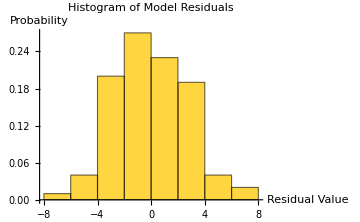

-Graphics-

-Graphics-

-Graphics-

```mathematica
SeedRandom[123];
sampleSize = 100;
X1 = RandomReal[{0, 10}, sampleSize];
X2 = RandomReal[{0, 10}, sampleSize];
X = {X1, X2};
Xt = Transpose[X];

Beta1 = 3.5;
Beta2 = -1.7;

noise = RandomVariate[NormalDistribution[0, 2.5], sampleSize];

Y = Beta1 * X1 + Beta2 * X2 + noise;
betaHat = Inverse[Transpose[Xt] . Xt] . Transpose[Xt] . Y;

b1 = betaHat[[1]];
b2 = betaHat[[2]];

Print["Calculated B1: ", b1];
Print["Calculated B2: ", b2];

Yhat = Xt . betaHat;
residuals = Y - Yhat;

data3D = Transpose[{X1, X2, Y}];
scatterPlot = ListPointPlot3D[data3D, PlotStyle -> {Red, PointSize[0.02]}, AxesLabel -> {"X1", "X2", "Y"}];
planePlot = Plot3D[b1 * x + b2 * z, {x, 0, 10}, {z, 0, 10}, PlotStyle -> Directive[Blue, Opacity[0.4]], Mesh -> None];
Show[scatterPlot, planePlot, PlotLabel -> "Linear Regression in 3D", ImageSize -> Medium]

Print["Correlation coefficient X1 and X2: ", Correlation[X1, X2]];
ListPlot[Transpose[{X1, X2}], AxesLabel -> {"X1", "X2"}, PlotLabel -> "Correlation Plot of X1 and X2", ImageSize -> Medium]

Histogram[residuals, Automatic, "Probability", PlotLabel -> "Histogram of Model Residuals", AxesLabel -> {"Residual Value", "Probability"}, ImageSize -> Medium]

ListPlot[residuals, PlotLabel -> "Dependence of residuals e_i on observation number i", AxesLabel -> {"i", "e_i"}, ImageSize -> Medium, GridLines -> Automatic]

ListPlot[Transpose[{Yhat, residuals}], PlotLabel -> "Dependence of residuals on predictions Y_hat", AxesLabel -> {"Y_hat", "e_i"}, ImageSize -> Medium]

ei1 = Drop[residuals, -1];
eip1 = Drop[residuals, 1];
ei2 = Drop[residuals, -2];
eip2 = Drop[residuals, 2];

ListPlot[{Transpose[{ei1, eip1}], Transpose[{ei2, eip2}]}, PlotLabel -> "Residual Autocorrelation Analysis", AxesLabel -> {"e_i", "e_{i+k}"}, PlotStyle -> {Blue, Orange}, PlotLegends -> {"e_{i+1}", "e_{i+2}"}, ImageSize -> Medium]
```